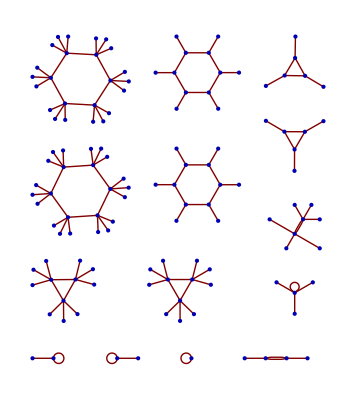

```mathematica
GraphPlot[Table[i->Mod[i^2,129],{i,0,128}]]
```

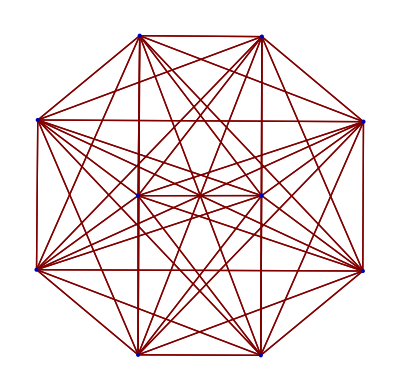

```mathematica
connections={};
GraphPlot[Table[i->j,{i,10},{j,10}]]
```

```mathematica
cores = Table[13 i+1,{i,0,3}];
coreEdge=Table[cores[[i]]->cores[[j]],{i,4},{j,i+1,4}];
l1=Table[Table[t+1+4 i,{i,0,2}],{t,cores}];
l1Edge=Table[Table[t->t+1+4 i,{i,0,2}],{t,cores}];
l2= Table[Table[t+i,{i,1,3}],{t,Flatten@l1}];
l2Edge=Table[Table[t->t+i,{i,1,3}],{t,Flatten@l1}];
```

```mathematica
coreEdge
```

{{1→14,1→27,1→40},{14→27,14→40},{27→40},{}}

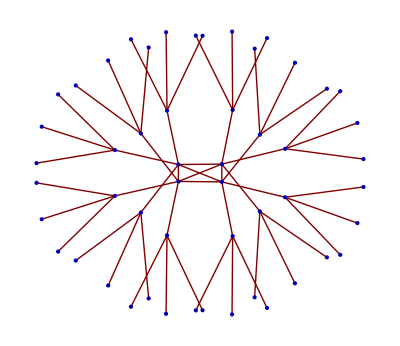

```mathematica
edges=Flatten[Join[coreEdge,l1Edge,l2Edge]];
GraphPlot[edges,Method->"SpringEmbedding"]
```

```mathematica
edges
```

{1→1,1→14,1→27,1→40,14→1,14→14,14→27,14→40,27→1,27→14,27→27,27→40,40→1,40→14,40→27,40→40,1→2,1→6,1→10,14→15,14→19,14→23,27→28,27→32,27→36,40→41,40→45,40→49,2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,15→16,15→17,15→18,19→20,19→21,19→22,23→24,23→25,23→26,28→29,28→30,28→31,32→33,32→34,32→35,36→37,36→38,36→39,41→42,41→43,41→44,45→46,45→47,45→48,49→50,49→51,49→52}

```mathematica
Table[t[[1]]==t[[2]],{t,edges}]
```

{True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}